# Answer to the Question 1

## part (a)

```mathematica
n=RandomInteger[{2020,999999}]
NextPrime[n]
For[i=1,Prime[i]≤n,i++]
Prime[i]
For[set={};i=1,i≤n,i++,If[Divisible[i,5]&&Divisible[i,6],set=AppendTo[set,i]]]
set
```

540837

540851

540851

{30,60,90,120,150,180,210,240,270,300,330,360,390,420,450,480,510,540,570,600,630,660,690,720,750,780,810,840,870,900,930,960,990,1020,1050,1080,1110,1140,1170,1200,1230,1260,1290,1320,1350,1380,1410,1440,1470,1500,1530,1560,1590,1620,1650,1680,17915,539160,539190,539220,539250,539280,539310,539340,539370,539400,539430,539460,539490,539520,539550,539580,539610,539640,539670,539700,539730,539760,539790,539820,539850,539880,539910,539940,539970,540000,540030,540060,540090,540120,540150,540180,540210,540240,540270,540300,540330,540360,540390,540420,540450,540480,540510,540540,540570,540600,540630,540660,540690,540720,540750,540780,540810}
 |  |  |  |

## part (b)

```mathematica
L1=Table[i^2,{i,99}]
L2=Table[2*i,{i,99}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801}

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198}

```mathematica
Union[L1,L2]
Intersection[L1,L2]
```

{1,2,4,6,8,9,10,12,14,16,18,20,22,24,25,26,28,30,32,34,36,38,40,42,44,46,48,49,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,81,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,121,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,169,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801}

{4,16,36,64,100,144,196}

# Answer to the Question 2

```mathematica
A=(-{{1, 3, 1}, {0, 1, 2}, {0, 0, 1}});
```

## Part (a)

```mathematica
Det[A]
```

-1

```mathematica
(*Since det(A)≠0, A^-1 exist*)
Inverse[A]//MatrixForm
```

(-1 | 3 | -5
0 | -1 | 2
0 | 0 | -1)

## Part (b)

```mathematica
Eigenvalues[A]
p=Eigenvectors[A]
```

{-1,-1,-1}

{{1,0,0},{0,0,0},{0,0,0}}

```mathematica
MatrixRank[p]
MatrixRank[A]
```

1

3

```mathematica
(*A is a square matrix of order 3, but there is only 1 eigen vectors of A. So its not possible to find and invertible matrix P*)
```

# Answerto the Question 3

## Part (a)

```mathematica
∑_(n=1)^∞ 1/(n*(n+1)*(n+2))
```

1/4

```mathematica
s=0;
Do[s=s+1/(i*(i+1)*(i+2)),{i,1,99}]
s
```

5049/20200

```mathematica
For[i=1;s=0,i≤99,i++,s=s+1/(i*(i+1)*(i+2))]
s
```

5049/20200

## Part (b)

```mathematica
Solve[x1+x2-2 x3==1&&2 x1-3 x2+x3==-8&&3 x1+x2+4 x3==7]
```

{{x1→0,x2→3,x3→1}}

```mathematica
M=({{1, 1, -2, 1}, {2, -3, +1, -8}, {3, 1, 4, 7}});
d=Det[M[[All,{1,2,3}]]];
d1=Det[M[[All,{4,2,3}]]];
d2=Det[M[[All,{1,4,3}]]];
d3=Det[M[[All,{1,2,4}]]];
```

```mathematica
{d1/d,d2/d,d3/d}
```

{0,3,1}

# Answer to the Question 4

## Part (a)

```mathematica
f[x_]:=-3 x+3/;x<1
f[x_]:=3 x-3/;1≤x≤5
f[x_]:=10/;x>5
```

Section (i)

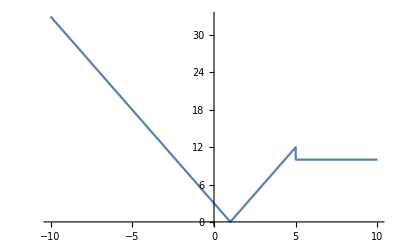

```mathematica
Plot[f[x],{x,-10,10}]
```

section (ii)

```mathematica
lhd=Limit[(f[1+h]-f[1])/h,h->0,Direction->-1];
rhd=Limit[(f[1+h]-f[1])/h,h->0,Direction->1];
lhd==rhd
```

Limit[f[1+h]/h,h→0,Direction→-1]==Limit[f[1+h]/h,h→0,Direction→1]

```mathematica
(*the function is not differentiable at x=1*)
```

Chapter (iii)

```mathematica
Solve[f[x]==0,x]
```

{{x→0}}

# Answer to the Question 5

```mathematica
Clear[f];
p=x^2-11 y^2-16 x y+10x+10 y-7;
a=1;b=-11;c=-7;
h=-8;g=5;f=5;
d1=Det[({{a, h, g}, {h, b, f}, {g, f, c}})]
d2=a b-h^2
d3=a+b
```

375

-75

-10

```mathematica
(*Since d1≠0,d2<0 and d3≠0, the equation represent a hyperbola*)
α=(f h-b g)/d2;
β=(g h-a f)/d2;
θ=(1/2)ArcTan[2*h/(a-b)];
(*Rotating the axes by angel θ and shifting the center to {α,β} to remove xy terms and x,y terms respectively*)
P=Expand[p/.x->X*Cos[θ]-Y*Sin[θ]+α/.y->X*Sin[θ]+Y*Cos[θ]+β//Simplify]
```

-5+5 X^2-15 Y^2

hence the equation be,
            5 X^2-15 Y^2-5=0;
=>5 X^2-15 Y^2=5;
=>(5 X^2-15 Y^2)/5=1;
=>X^2/1-Y^2/(1/3)=1;
Which is the standard form of the conic

```mathematica
(* Computiong the equation of transformed axes with respect to original axes*)
var=Expand[Solve[x==X*Cos[θ]-Y*Sin[θ]+α&&y==X*Sin[θ]+Y*Cos[θ]+β,{X,Y}]]//N
```

{{X→0.447214+0.894427 x-0.447214 y,Y→-0.447214+0.447214 x+0.894427 y}}

```mathematica
X1=var[[1,1,2]];
Y1=var[[1,2,2]];
(*Comparing X^2/4-Y^2/9=1 with the standard equation of hyperbola*)
A=2;
B=3;
e=Sqrt[1-(A^2/B^2)];
```

```mathematica
(*centre*)
Solve[X1==Y1==0,{x,y}]
```

{{x→-0.2,y→0.6}}

```mathematica
(*focus of the Hyperbola*)
p1=Solve[X1==A*e&&Y1==0,{x,y}]
p2=Solve[X1==-A*e&&Y1==0,{x,y}]
```

{{x→1.13333,y→-0.0666667}}

{{x→-1.53333,y→1.26667}}

```mathematica
q=p-c-g α-f β
```

-2+10 x+x^2+10 y-16 x y-11 y^2

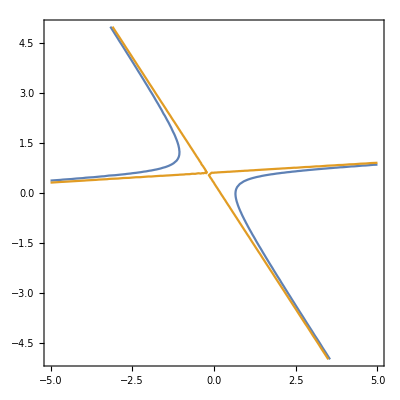

```mathematica
ContourPlot[{p==0,q==0},{x,-5,5},{y,-5,5}]
```

```mathematica
Factor[q]
```

-2+10 x+x^2+10 y-16 x y-11 y^2

# Answer to the Question 6

```mathematica
Print["Volume=",π*∫_0^2 8xⅆx//N]
```

Volume=50.2655